#### Docked cell

```mathematica
CurrentValue[EvaluationNotebook[],DockedCells]={};
```

```mathematica
DeveloperDockedCell//ClearAll
DeveloperDockedCell[package_String,path_]/;StringMatchQ[package,__~~"`"~~__~~"`"]:=(
CurrentValue[EvaluationNotebook[],DockedCells]={
Cell[BoxData[ToBoxes[DynamicModule[{
name=First@StringCases[package,__~~"`"~~name__~~"`":>name],
time=0,paclet="",url=None,progress="",withProgress
},
withProgress=Function[,progress=ProgressIndicator[Appearance->"Necklace"];#;progress=Quantity[time,"Seconds"],HoldAll];
Grid[{
{
Column[{
Button["Reload code",
time=First@AbsoluteTiming[
Module[{pacletDirectory},
Quiet@ClearAll[package<>"`*",package<>"`**`*"];
PacletDirectoryLoad[path];
];
Get[package];
];//withProgress
],
Button["Reload paclet",
time=First@AbsoluteTiming[
<<PacletTools`;
paclet=Quiet@PacletTools`PacletBuild[path]["PacletArchive"];
PacletInstall[paclet,ForceVersionInstall->True];
Get[package]
];//withProgress,
Method->"Queued"
]}],
Dynamic[Column@{ClickToCopy[FileNameTake[paclet],paclet],progress},TrackedSymbols:>{paclet,progress}]
},
{
Button["Upload paclet",
time=First@AbsoluteTiming[
CloudObject`Private`$allowInternetCheck=True;
DeleteFile[CloudObject[name<>".paclet"]];
url=URLShorten@CopyFile[File[paclet],CloudObject[name<>".paclet",Permissions->"Public"]]
];//withProgress,
Method->"Queued"
],
Dynamic[$CloudUserID],
Dynamic[ClickToCopy@url]
}
},Alignment->Left]]]]
]
};
)
```

```mathematica
DeveloperDockedCell["Wolfram`QuantumFramework`",FileNameJoin[{NotebookDirectory[],"..","QuantumFramework"}]]
```

```mathematica
CloudDeploy[DefineResourceFunction[DeveloperDockedCell],CloudObject["DeveloperDockedCell",Permissions->"Public"]]
```

CloudObject[https://www.wolframcloud.com/obj/nikm/DeveloperDockedCell]

### Build

```mathematica
(*Quiet@Remove["*`Quantum*"]

ClearAll["Wolfram`QuantumFramework`*","Wolfram`QuantumFramework`**`*"]
PacletUninstall[PacletFind["*QuantumFramework*"]];*)
If[FileExistsQ[paclet],DeleteFile[paclet]];
pacletDirectory=ExpandFileName@FileNameJoin[{NotebookDirectory[],"..","QuantumFramework"}];
CreatePacletArchive[pacletDirectory]
paclet=RenameFile[%,ExpandFileName@FileNameJoin[{NotebookDirectory[],"..","QuantumFramework","build",FileNameTake[%]}],OverwriteTarget->True]
PacletInstall[paclet,ForceVersionInstall->True]
```

```mathematica
<<Wolfram`QuantumFramework`
```

```mathematica
Quit
```

```mathematica
<<PacletTools`;
paclet=Echo@PacletTools`PacletBuild[ExpandFileName@FileNameJoin[{NotebookDirectory[],"..","QuantumFramework"}]]["PacletArchive"];
PacletInstall[paclet,ForceVersionInstall->True]
```

```mathematica
Button["Reload paclet",

<<PacletTools`;
paclet=Echo@Quiet@PacletTools`PacletBuild[ExpandFileName@FileNameJoin[{NotebookDirectory[],"..","QuantumFramework"}]]["PacletArchive"];
PacletInstall[paclet,ForceVersionInstall->True]
]
```

Reload paclet

### Config

```mathematica
Wolfram`QuantumFramework`PackageScope`$QuantumFrameworkPropCache=False
Wolfram`QuantumFramework`PackageScope`$QuantumFrameworkProfile=False
```

False

False

### AutoCompletion generation

```mathematica
Get@ExpandFileName@FileNameJoin[{NotebookDirectory[],"..","Scripts","GenerateAutoCompletion.wl"}]
```

### Usage

```mathematica
usage = Map[file |->
	Block[{nb = NotebookOpen[file, Visible -> False], usage},
		NotebookFind[nb, "Usage", Next, CellStyle];
		usage = FileBaseName[file] <> "::usage = " <> ExportString[ToString[RawBoxes[NotebookRead[nb]], StandardForm], "WL", "Comments" -> None];
		NotebookClose[nb];
		usage
	],
	FileNames[ExpandFileName @ FileNameJoin[{NotebookDirectory[], "..", "QuantumFramework", "build", "Wolfram__QuantumFramework", "Documentation", "English", "ReferencePages", "Symbols", "*"}]][[;;]]
];
With[{file = File[ExpandFileName @ FileNameJoin[{NotebookDirectory[], "..", "QuantumFramework", "Kernel", "Usage.m"}]]},
	BinaryWrite[
		file,
		StringRiffle[{"Package[\"Wolfram`QuantumFramework`\"]", Splice[usage]}, "\r\n\r\n\r\n"]
	];
	Close[file];
]
```

```mathematica
Scan[If[!CurrentValue[#,Visible],NotebookClose[#]]&,Notebooks[]]
```

### Upload

```mathematica
CloudObject`Private`$allowInternetCheck=True;
DeleteFile[CloudObject["QuantumFramework.paclet"]];
url=URLShorten@CopyFile[File[paclet],CloudObject["QuantumFramework.paclet",Permissions->"Public"]]
```

https://wolfr.am/11hS8AMYL

```mathematica
redirectCloudDeployedPaclet // ClearAll;
redirectCloudDeployedPaclet // Attributes = { HoldRest };
redirectCloudDeployedPaclet[ obj_CloudObject, target_ResourceObject ] := 
    Block[ { ResourceObject },
        SetAttributes[ ResourceObject, HoldAllComplete ];
        CloudPut[
            target,
            FileNameJoin @ { obj, "Resource.wl" },
            Permissions -> "Public"
        ];
        obj
    ];
```

```mathematica
redirectCloudDeployedPaclet[
CloudObject["DeployedResources/Paclet/Wolfram/QuantumFramework"],
ResourceObject["Wolfram/QuantumFramework"]
]
```

CloudObject[https://www.wolframcloud.com/obj/wolframquantumframework/DeployedResources/Paclet/Wolfram/QuantumFramework]

```mathematica
Quit
```

```mathematica
PacletInstall["https://wolfr.am/DevWQCF"]
```

PacletObject[…]

### Submit

PacletFileChanged error workaround

```mathematica
DefinitionNotebookClient`PackageScope`$FailureLevels=ReplacePart[DefinitionNotebookClient`PackageScope`$FailureLevels,{{"Paclet","PacletFileChanged",_,"Submit"|"SubmitUpdate"}->"Waning",{"Paclet","NoPacletInfoFileCell"}->"Waning"}];
```

### Style

```mathematica
SetOptions[EvaluationNotebook[],StyleDefinitions->Notebook@{
Cell[StyleData[StyleDefinitions->"Default.nb"]],
Cell[StyleData["Quantum",StyleDefinitions->StyleData["Input"]],DefaultFormatType->TraditionalForm,ShowStringCharacters->False,FontWeight->Plain,MenuCommandKey->"_"]}]
```

### Stash

```mathematica
QSP[phi0_, phis__] := QuantumCircuitOperator[{{"RZ", - 2 phi0}, Table[{{"RX", - 2 ArcCos[a]}, {"RZ", - 2 phi}}, {phi, {phis}}]}]["CircuitOperator"]["Simplify"]
```

```mathematica
Table[
{
Abs@ChebyshevT[n,a],
Assuming[-1<a<1,FullSimplify@Sqrt@TrigExpand@FullSimplify[QuantumState["0"]["Dagger"][(QSP@@Table[0,n+1])@QuantumState["0"]]["Norm"]^2]]
},
{n,6}
]
```

{{Abs[a],Abs[a]},{Abs[-1+2 a^2],Abs[1-2 a^2]},{Abs[-3 a+4 a^3],Abs[3 a-4 a^3]},{Abs[1-8 a^2+8 a^4],Abs[1-8 a^2+8 a^4]},{Abs[5 a-20 a^3+16 a^5],Abs[5 a-20 a^3+16 a^5]},{Abs[-1+18 a^2-48 a^4+32 a^6],Abs[1-2 a^2 (3-4 a^2)^2]}}

```mathematica
QuantumOperator[{"HeisenbergWeyl",1,1,a2}]
```

QuantumOperator[…]

```mathematica
QuantumCircuitOperator[{"H","CNOT","T"->2,"Barrier","S"}]
```

QuantumCircuitOperator[…]

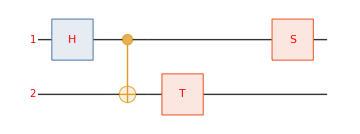

```mathematica
QuantumCircuitOperator[{"H","CNOT","T"->2,"Barrier","S"}]["Diagram",FontColor->Red,"BarrierStyle"->Transparent,"WireStyle"->Directive[Thick,Black,Opacity[.8]]]
```

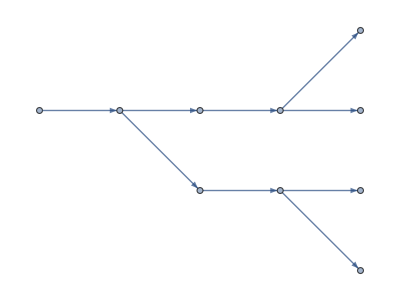

```mathematica
CircuitMultiwayGraph[QuantumCircuitOperator[{"H","CNOT","RandomUnitary"->2,"CNOT"->{2,3}}],EdgeStyle->Thick]
```

## Code

#### experimental

```mathematica
QuantumWignerTransformGraph // ClearAll
QuantumWignerTransformGraph[obj_, opts : OptionsPattern[]] := With[{dcmp = QuantumWignerTransform[obj]["Decompose"]},
	SimpleGraph[
		Catenate @ Map[
			With[{partition = Partition[#, Length[#] / 2]},
				Join[
					Catenate[Annotation[UndirectedEdge[##], EdgeStyle -> Blue] & @@@ Tuples[#, 2] & /@ partition],
					MapThread[Annotation[UndirectedEdge[##], EdgeStyle -> Red] &, partition]
				]
			] &,
			dcmp
		],
		opts,
		VertexShapeFunction -> (Inset[Framed[Show[#2["BlochPlot"] /. _Text -> Nothing, ImageSize -> 32]], #1, #3] &),
		PerformanceGoal -> "Quality"
	]
]
```

```mathematica
bipartitionDimension[dim : _Integer | Automatic : Automatic, qudits_Integer, dims : {_Integer..}] := Replace[dim, Automatic -> If[
        qudits > 1,
        First @ dims,
        Replace[Divisors[Times @@ dims], {{1, d_} :> d, {___, d_, _} :> d}]
    ]]

QuantumOperatorSchmidtBasis // ClearAll
QuantumOperatorSchmidtBasis[op_, outDim : _Integer | Automatic : Automatic, inDim : _Integer | Automatic : Automatic] /;
	(outDim === Automatic || Divisible[op["OutputDimension"], outDim]) && (inDim === Automatic || Divisible[op["InputDimension"], inDim]) :=
With[{
	schmidtState = op["SchmidtBasis", op["OutputDimension"]]["SplitDual", 1],
	n = bipartitionDimension[outDim, op["OutputQudits"], op["OutputDimensions"]],
	m = bipartitionDimension[inDim, op["InputQudits"], op["InputDimensions"]]
},
	QuantumOperator @ QuantumState[schmidtState, Echo@QuantumBasis[schmidtState["Output"]["DimensionSplit", 1, n], schmidtState["Input"]["Dual"]["DimensionSplit", 1, m]]]
]
```

#### IBMQ

```mathematica
<<PacletTools`;
PacletUninstall/@PacletFind["*IBMQ*"];
paclet=PacletTools`PacletBuild[FileNameJoin[{NotebookDirectory[],"..","IBMQ"}]]["PacletArchive"];
PacletInstall[paclet,ForceVersionInstall->True]
RenameFile[paclet,FileNameJoin[{NotebookDirectory[],"..","QuantumFramework","Assets",FileNameTake[paclet]}],OverwriteTarget->True];
```

PacletObject[…]

```mathematica
Scan[DeleteObject,PersistentObjects["*/Once/*","KernelSession"]]
```

```mathematica
Get@FileNameJoin[{PacletFind["*IBMQ*"][[1]]["Location"],"Kernel","IBMQ.m"}];
```

```mathematica
auth=URLExecute[HTTPRequest["https://auth.quantum-computing.ibm.com/api/users/loginWithToken",<|Method->"POST","Body"-><|"apiToken"->|>|>]];
```

```mathematica
ibm=ServiceConnect["IBMQ",Authentication->auth,"DeletePreviousConnections"->True]
```

```mathematica
ibm=ServiceConnect["IBMQ","New"]
```

ServiceObject[…]

#### Cotengra

```mathematica
<<PacletTools`;
paclet=PacletTools`PacletBuild[FileNameJoin[{NotebookDirectory[],"..","Cotengra"}]]["PacletArchive"];
PacletInstall[paclet,ForceVersionInstall->True]
Quiet@CreateDirectory[FileNameJoin[{NotebookDirectory[],"..","QuantumFramework","Assets"}]];
RenameFile[paclet,FileNameJoin[{NotebookDirectory[],"..","QuantumFramework","Assets",FileNameTake[paclet]}],OverwriteTarget->True];
```

PacletObject[…]

#### QASM

import sys
path = <* ExpandFileName @ FileNameJoin[{NotebookDirectory[], "..", "QASM"}] *>
if path not in sys.path:
	sys.path.append(path)

from antlr4 import *
from qasm3Lexer import qasm3Lexer
from qasm3Parser import qasm3Parser
from qasm3ParserVisitor import qasm3ParserVisitor

class qasm3Visitor(ParseTreeVisitor):
	def visitProgram(self, ctx):
		return [statement.gateCallStatement().Identifier().getText() for statement in ctx.statement() if statement.gateCallStatement()]
	def visitVersion(self, ctx:qasm3Parser.VersionContext):
		return ctx.version().VersionSpecifier().getText()
	def visitGateCallStatement(self, ctx):
		return 2

data = InputStream('''OPENQASM 3.0;
qubit[2] q;
bit[0] c;
U(0., 0., 1.5708) q[0], q[1];
U(1.5708, 0., 3.14159) q[1];
ctrl(1) @ negctrl(0) @ U(3.14159, 0., 3.14159) q[1], q[0];
''')
# lexer
lexer = qasm3Lexer(data)
stream = CommonTokenStream(lexer)
# parser
parser = qasm3Parser(stream)
tree = parser.program()
# evaluator
visitor = qasm3Visitor()
visitor.visitProgram(tree)
#dir(tree.getChild(0)), tree.getChild(0).getChild(1).getPayload()

#### NN

```mathematica
Quit
```

```mathematica
PacletDirectoryLoad["~/src/wolfram/neuralnetworks/NeuralNetworks"]
```

{/Users/swish/src/wolfram/QuantumComputing/QuantumFramework,/Users/swish/src/wolfram/neuralnetworks/NeuralNetworks}

```mathematica
<<NeuralNetworks`
```

General::mxnetlinkver: The wrong version of MXNetLink was loaded from path /Applications/Wolfram Desktop.app/Contents/SystemFiles/Components/MXNetLink (loaded version 14.1.0, expected version {14.0.0}). This might lead to unexpected problems.

```mathematica
iShape={1,2,3,4,5,4,3,2,1};
l=TransposeLayer[{1,8,7,2,3,9,4,5,6},"Input"->iShape];
Dimensions[l@RandomReal[1,iShape]]=={1,4,5,3,2,1,3,2,4}
```

TransposeLayer::valfail: Validation failed for TransposeLayer: arrays with rank higher than 5 are not fully supported for transposition

False

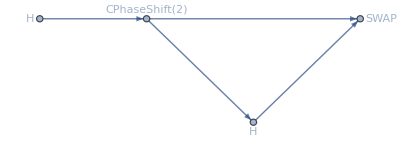

{{1,2},{1,2},{1,2}}

```mathematica
net=FullSimplify[QuantumWignerTransform[QuantumCircuitOperator[{"Fourier",2}]]]["TensorNetwork","Computational"->False,"PrependInitial"->False]
path=TensorNetworkContractionPath@net
```

```mathematica
nn=TensorNetworkNetGraph[net,path]
```

NetGraph[…]

```mathematica
nn[]==QuantumWignerTransform[QuantumCircuitOperator[{"Fourier",2}]]["Tensor"]
```

True

### CHSH phase space

```mathematica
doubleCHSH=QuantumWignerTransform[QuantumCircuitOperator[{
QuantumCircuitOperator[{"+"->2,"+"->3},"Charlie"],
"Cup"->{1,4},
"RY"[Pi/4]->4,
"C0"["H"]->{3,4},
"C"["H"]->{2,1}(*,
"Measure"->1,"Measure"->4*)
}]]["Flatten"]["FullSimplify"]
```

QuantumCircuitOperator[…]

```mathematica
g=QuantumCircuitMultiwayGraph[doubleCHSH,GraphLayout->"LayeredDigraphEmbedding",EdgeLabels->__tag_:>Framed[tag["Operator"]["CircuitDiagram","WireLabels"->None,"ShowGateLabels"->False,"ShowEmptyWires"->False,FontSize->8,ImageSize->{32,32}],Background->White],PerformanceGoal->"Quality"];
```

```mathematica
Total[TensorProduct@@@Map[#["PhaseSpace"]&,VertexList[g][[-16;;,2]],{2}]]
```

SparseArray[…]

```mathematica
N@doubleCHSH[]
```

0.0078125W_00 W_00 W_00 W_00+0.00552427W_00 W_00 W_01 W_01+0.00552427W_00 W_00 W_01 W_10+0.00390625W_00 W_01 W_00 W_01+0.00390625W_00 W_01 W_00 W_10+0.00552427W_00 W_01 W_01 W_00-0.00390625W_00 W_01 W_10 W_01+0.00390625W_00 W_01 W_10 W_10-0.00552427W_00 W_01 W_11 W_11+0.00276214W_01 W_00 W_00 W_01+0.00276214W_01 W_00 W_00 W_10+0.00390625W_01 W_00 W_01 W_00-0.00276214W_01 W_00 W_10 W_01+0.00276214W_01 W_00 W_10 W_10-0.00390625W_01 W_00 W_11 W_11+0.00552427W_01 W_01 W_00 W_00+0.00390625W_01 W_01 W_01 W_01+0.00390625W_01 W_01 W_01 W_10-0.00276214W_01 W_10 W_00 W_01-0.00276214W_01 W_10 W_00 W_10-0.00390625W_01 W_10 W_01 W_00-0.00276214W_01 W_10 W_10 W_01+0.00276214W_01 W_10 W_10 W_10-0.00390625W_01 W_10 W_11 W_11-0.00552427W_01 W_11 W_10 W_11+0.00390625W_01 W_11 W_11 W_01-0.00390625W_01 W_11 W_11 W_10+0.00276214W_10 W_00 W_00 W_01+0.00276214W_10 W_00 W_00 W_10+0.00390625W_10 W_00 W_01 W_00-0.00276214W_10 W_00 W_10 W_01+0.00276214W_10 W_00 W_10 W_10-0.00390625W_10 W_00 W_11 W_11+0.00552427W_10 W_01 W_00 W_00+0.00390625W_10 W_01 W_01 W_01+0.00390625W_10 W_01 W_01 W_10+0.00276214W_10 W_10 W_00 W_01+0.00276214W_10 W_10 W_00 W_10+0.00390625W_10 W_10 W_01 W_00+0.00276214W_10 W_10 W_10 W_01-0.00276214W_10 W_10 W_10 W_10+0.00390625W_10 W_10 W_11 W_11+0.00552427W_10 W_11 W_10 W_11-0.00390625W_10 W_11 W_11 W_01+0.00390625W_10 W_11 W_11 W_10+0.0078125W_11 W_10 W_10 W_11-0.00552427W_11 W_10 W_11 W_01+0.00552427W_11 W_10 W_11 W_10-0.00390625W_11 W_11 W_00 W_01-0.00390625W_11 W_11 W_00 W_10-0.00552427W_11 W_11 W_01 W_00-0.00390625W_11 W_11 W_10 W_01+0.00390625W_11 W_11 W_10 W_10-0.00552427W_11 W_11 W_11 W_11

```mathematica
Total[QuantumTensorProduct/@N@VertexList[g][[-16;;,2]]]//Chop
```

0.853553u_1 v_1 u_1 v_1+0.204124u_1 v_1 u_2 v_2+0.218218u_1 v_1 u_2 v_3+0.188982u_1 v_1 u_2 v_4-0.0976311u_1 v_1 u_3 v_2+0.185817u_1 v_1 u_3 v_3-0.109109u_1 v_1 u_3 v_4-0.0690356u_1 v_1 u_4 v_2-0.152081u_1 v_1 u_4 v_3+0.250175u_1 v_1 u_4 v_4+0.353553u_2 v_2 u_1 v_1-0.204124u_2 v_2 u_2 v_2-0.218218u_2 v_2 u_2 v_3-0.188982u_2 v_2 u_2 v_4+0.235702u_2 v_2 u_3 v_2-0.259619u_2 v_2 u_3 v_3+0.0451944u_2 v_2 u_3 v_4+0.166667u_2 v_2 u_4 v_2+0.0998952u_2 v_2 u_4 v_3-0.29537u_2 v_2 u_4 v_4-0.327327u_2 v_3 u_2 v_3+0.377964u_2 v_3 u_2 v_4-0.166667u_2 v_3 u_3 v_2-0.178174u_2 v_3 u_3 v_3-0.154303u_2 v_3 u_3 v_4+0.235702u_2 v_3 u_4 v_2+0.251976u_2 v_3 u_4 v_3+0.218218u_2 v_3 u_4 v_4-0.327327u_3 v_2 u_2 v_3+0.377964u_3 v_2 u_2 v_4-0.166667u_3 v_2 u_3 v_2-0.178174u_3 v_2 u_3 v_3-0.154303u_3 v_2 u_3 v_4+0.235702u_3 v_2 u_4 v_2+0.251976u_3 v_2 u_4 v_3+0.218218u_3 v_2 u_4 v_4+0.353553u_3 v_3 u_1 v_1-0.204124u_3 v_3 u_2 v_2-0.218218u_3 v_3 u_2 v_3-0.188982u_3 v_3 u_2 v_4+0.235702u_3 v_3 u_3 v_2-0.259619u_3 v_3 u_3 v_3+0.0451944u_3 v_3 u_3 v_4+0.166667u_3 v_3 u_4 v_2+0.0998952u_3 v_3 u_4 v_3-0.29537u_3 v_3 u_4 v_4+0.146447u_4 v_4 u_1 v_1-0.204124u_4 v_4 u_2 v_2-0.218218u_4 v_4 u_2 v_3-0.188982u_4 v_4 u_2 v_4-0.569036u_4 v_4 u_3 v_2+0.170532u_4 v_4 u_3 v_3+0.417716u_4 v_4 u_3 v_4-0.402369u_4 v_4 u_4 v_2+0.404057u_4 v_4 u_4 v_3-0.0319573u_4 v_4 u_4 v_4

```mathematica
Total[TensorProduct@@@Map[QuantumState[#,"Wigner"[2,"Exact"->False],"Picture"->"PhaseSpace"]["PhaseSpace"]&,VertexList[g][[-16;;,2]],{2}]]
```

SparseArray[<27648>, {4, 4, 4, 4, 4, 4, 4, 4}]

```mathematica
QuantumCircuitOperator[{
QuantumCircuitOperator[{"+"->2,"+"->3},"Charlie"],
"Cup"->{1,4},
"RY"[Pi/4]->4,
"C0"["H"]->{3,4},
"C"["H"]->{2,1}(*,
"Measure"->1,"Measure"->4*)
}][]["Probability"]//N
```

<|0000→0.106694,0001→0.0183058,0010→0.106694,0011→0.0183058,0100→0.106694,0101→0.0183058,0110→0.0183058,0111→0.106694,1000→0.0183058,1001→0.106694,1010→0.0183058,1011→0.106694,1100→0.0183058,1101→0.106694,1110→0.106694,1111→0.0183058|>

```mathematica
Total[TensorProduct@@@Map[QuantumState[#,"Wigner"[2,"Exact"->False],"Picture"->"PhaseSpace"]["PhaseSpace"]&,VertexList[g][[-16;;,2]],{2}]]
```

SparseArray[<27648>, {4, 4, 4, 4, 4, 4, 4, 4}]

```mathematica
Fold[Total[#1,{#2}]&,Total[TensorProduct@@@Map[QuantumState[#,"Wigner"[2,"Exact"->False],"Picture"->"PhaseSpace"]["PhaseSpace"][[;;2,;;2]]&,VertexList[g][[-16;;,2]],{2}]],Range[4]]
```

SparseArray[…]

```mathematica
Fold[Total[#1,{#2}]&,Total[TensorProduct@@@Map[QuantumState[#,"Wigner"[2,"Exact"->False],"Picture"->"PhaseSpace"]["PhaseSpace"][[;;2,;;2]]&,VertexList[g][[-16;;,2]],{2}]],Range[4]][[;;;;2,;;;;2,;;;;2,;;;;2]]/2//Flatten//Normal
```

{0.106694+0. ⅈ,0.0183058+0. ⅈ,0.106694+0. ⅈ,0.0183058+0. ⅈ,0.106694+0. ⅈ,0.0183058+0. ⅈ,0.0183058+0. ⅈ,0.106694+0. ⅈ,0.0183058+0. ⅈ,0.106694+0. ⅈ,0.0183058+0. ⅈ,0.106694+0. ⅈ,0.0183058+0. ⅈ,0.106694+0. ⅈ,0.106694+0. ⅈ,0.0183058+0. ⅈ}

```mathematica
Values@N@doubleCHSH[]["Computational"]["Probability"]
```

{0.0113836,0.00195313,0.00195313,0.000335103,0.0113836,0.00195313,0.00195313,0.000335103,0.0113836,0.00195313,0.00195313,0.000335103,0.0113836,0.00195313,0.00195313,0.000335103,0.0113836,0.00195313,0.00195313,0.000335103,0.00195313,0.0113836,0.000335103,0.00195313,0.0113836,0.00195313,0.00195313,0.000335103,0.00195313,0.0113836,0.000335103,0.00195313,0.0113836,0.00195313,0.00195313,0.000335103,0.0113836,0.00195313,0.00195313,0.000335103,0.00195313,0.000335103,0.0113836,0.00195313,0.00195313,0.000335103,0.0113836,0.00195313,0.0113836,0.00195313,0.00195313,0.000335103,0.00195313,0.0113836,0.000335103,0.00195313,0.00195313,0.000335103,0.0113836,0.00195313,0.000335103,0.00195313,0.00195313,0.0113836,0.00195313,0.0113836,0.000335103,0.00195313,0.00195313,0.0113836,0.000335103,0.00195313,0.00195313,0.0113836,0.000335103,0.00195313,0.00195313,0.0113836,0.000335103,0.00195313,0.00195313,0.0113836,0.000335103,0.00195313,0.0113836,0.00195313,0.00195313,0.000335103,0.00195313,0.0113836,0.000335103,0.00195313,0.0113836,0.00195313,0.00195313,0.000335103,0.00195313,0.0113836,0.000335103,0.00195313,0.00195313,0.0113836,0.000335103,0.00195313,0.000335103,0.00195313,0.00195313,0.0113836,0.000335103,0.00195313,0.00195313,0.0113836,0.00195313,0.0113836,0.000335103,0.00195313,0.0113836,0.00195313,0.00195313,0.000335103,0.000335103,0.00195313,0.00195313,0.0113836,0.00195313,0.000335103,0.0113836,0.00195313,0.00195313,0.000335103,0.0113836,0.00195313,0.00195313,0.000335103,0.0113836,0.00195313,0.00195313,0.000335103,0.0113836,0.00195313,0.00195313,0.000335103,0.0113836,0.00195313,0.00195313,0.000335103,0.0113836,0.00195313,0.000335103,0.00195313,0.00195313,0.0113836,0.00195313,0.000335103,0.0113836,0.00195313,0.000335103,0.00195313,0.00195313,0.0113836,0.00195313,0.000335103,0.0113836,0.00195313,0.00195313,0.000335103,0.0113836,0.00195313,0.0113836,0.00195313,0.00195313,0.000335103,0.0113836,0.00195313,0.00195313,0.000335103,0.00195313,0.000335103,0.0113836,0.00195313,0.000335103,0.00195313,0.00195313,0.0113836,0.0113836,0.00195313,0.00195313,0.000335103,0.00195313,0.0113836,0.000335103,0.00195313,0.000335103,0.00195313,0.00195313,0.0113836,0.000335103,0.00195313,0.00195313,0.0113836,0.000335103,0.00195313,0.00195313,0.0113836,0.000335103,0.00195313,0.00195313,0.0113836,0.000335103,0.00195313,0.00195313,0.0113836,0.00195313,0.000335103,0.0113836,0.00195313,0.000335103,0.00195313,0.00195313,0.0113836,0.00195313,0.000335103,0.0113836,0.00195313,0.000335103,0.00195313,0.00195313,0.0113836,0.000335103,0.00195313,0.00195313,0.0113836,0.00195313,0.0113836,0.000335103,0.00195313,0.00195313,0.0113836,0.000335103,0.00195313,0.000335103,0.00195313,0.00195313,0.0113836,0.00195313,0.000335103,0.0113836,0.00195313,0.00195313,0.0113836,0.000335103,0.00195313,0.0113836,0.00195313,0.00195313,0.000335103}

```mathematica
With[{g=QuantumCircuitMultiwayGraph[doubleCHSH,GraphLayout->"LayeredDigraphEmbedding",EdgeLabels->__tag_:>Framed[tag["Operator"]["CircuitDiagram","WireLabels"->None,"ShowGateLabels"->False,"ShowEmptyWires"->False,FontSize->8,ImageSize->{32,32}],Background->White],PerformanceGoal->"Quality"]},
Graph[g,VertexShapeFunction->((v|->v->Function[Inset[Grid[{MatrixPlot[#["PhaseSpace"][[;;2,;;2]],ImageSize->16,Frame->False]&/@#2[[2]]},Frame->All],#1,#3]])/@VertexList[g][[-16;;]])]
]
```

-Graphics-

```mathematica
With[{g=QuantumCircuitMultiwayGraph[doubleCHSH,GraphLayout->"LayeredDigraphEmbedding",EdgeLabels->__tag_:>Framed[tag["Operator"]["CircuitDiagram","WireLabels"->None,"ShowGateLabels"->False,"ShowEmptyWires"->False,FontSize->8,ImageSize->{32,32}],Background->White],PerformanceGoal->"Quality"]},
Graph[g,VertexShapeFunction->((v|->v->Function[Inset[Grid[With[{space=#["QuasiProbability"][[;;2,;;2]]},MatrixPlot[Clip[space,#],ImageSize->16,Frame->False]&/@{{0,1},{-1,0}}]&/@#2[[2]]//Transpose,Frame->All],#1,#3]])/@VertexList[g][[-16;;]])]
]
```

-Graphics-

Decomposition of a qubit into its positive and negative phase components is analogous to representation of logical qubits as multiple physical qubits with error correction codes, but in this case it is a sum instead of a product.

```mathematica
With[{states=VertexList[QuantumCircuitMultiwayGraph[doubleCHSH,GraphLayout->"LayeredDigraphEmbedding",EdgeLabels->__tag_:>Framed[tag["Operator"]["CircuitDiagram","WireLabels"->None,"ShowGateLabels"->False,"ShowEmptyWires"->False,FontSize->8,ImageSize->{32,32}],Background->White],PerformanceGoal->"Quality"]][[-16;;]]},
Grid[Partition[Row[With[{space=#["QuasiProbability"][[;;2,;;2]]},MatrixPlot[space,ImageSize->16,Frame->False]]&/@#[[2]],Frame->All]&/@states,4],
Frame->All,Spacings->{2,2}
]
]
```

-Graphics--Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics--Graphics-

```mathematica
With[{states=VertexList[QuantumCircuitMultiwayGraph[doubleCHSH,GraphLayout->"LayeredDigraphEmbedding",EdgeLabels->__tag_:>Framed[tag["Operator"]["CircuitDiagram","WireLabels"->None,"ShowGateLabels"->False,"ShowEmptyWires"->False,FontSize->8,ImageSize->{32,32}],Background->White],PerformanceGoal->"Quality"]][[-16;;]]},
Grid[Partition[Column[Insert[Grid[{#},Frame->All]&/@Transpose[With[{space=#["QuasiProbability"][[;;2,;;2]]},MatrixPlot[Clip[space,#],ImageSize->16,Frame->False]&/@{{0,1},{-1,0}}]&/@#[[2]]],"+",2],Alignment->Center,Spacings->0]&/@states,4],
Frame->All,Spacings->{2,2}
]
]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
+
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
+
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
+
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
+
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
+
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
+
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
+
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
+
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
+
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
+
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
+
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
+
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
+
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
+
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
+
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
+
-Graphics- | -Graphics- | -Graphics- | -Graphics-

Measurement sums over rows, which always end up

```mathematica
With[{states=VertexList[QuantumCircuitMultiwayGraph[doubleCHSH/*Table["Measure"->i,{i,4}],GraphLayout->"LayeredDigraphEmbedding",EdgeLabels->__tag_:>Framed[tag["Operator"]["CircuitDiagram","WireLabels"->None,"ShowGateLabels"->False,"ShowEmptyWires"->False,FontSize->8,ImageSize->{32,32}],Background->White],PerformanceGoal->"Quality"]][[-16;;,2]]},
Grid[Partition[Grid[{With[{space=#["QuasiProbability"][[;;2,;;2]]},MatrixPlot[space,ImageSize->16,Frame->False]]&/@#},Frame->All]&/@states,4],
Frame->All,Spacings->{2,2}
]
]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
With[{states=VertexList[QuantumCircuitMultiwayGraph[doubleCHSH/*Table["Measure"->i,{i,4}],GraphLayout->"LayeredDigraphEmbedding",EdgeLabels->__tag_:>Framed[tag["Operator"]["CircuitDiagram","WireLabels"->None,"ShowGateLabels"->False,"ShowEmptyWires"->False,FontSize->8,ImageSize->{32,32}],Background->White],PerformanceGoal->"Quality"]][[-16;;,2]]},
Grid[Partition[Grid[{With[{space=DiagonalMatrix[Total[#["QuasiProbability"]][[;;;;2]]]},MatrixPlot[space,ImageSize->16,Frame->False]]&/@#},Frame->All]&/@states,4],
Frame->All,Spacings->{2,2}
]
]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Notice that in the third column of branches second qubit is always degenerate, meaning these branches are actually reached a dead end and can’t contribute to our observable state anymore:

```mathematica
With[{states=VertexList[QuantumCircuitMultiwayGraph[doubleCHSH/*Table["Measure"->i,{i,4}],GraphLayout->"LayeredDigraphEmbedding",EdgeLabels->__tag_:>Framed[tag["Operator"]["CircuitDiagram","WireLabels"->None,"ShowGateLabels"->False,"ShowEmptyWires"->False,FontSize->8,ImageSize->{32,32}],Background->White],PerformanceGoal->"Quality"]][[-16;;,2]]},
Grid[Partition[MatrixPlot[Partition[Values@QuantumTensorProduct[#]["Computational"]["Amplitudes"],4],ImageSize->32,Frame->False]&/@states,4],
Frame->All,Spacings->{2,2}
]
]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

(p_1+n_1)×(p_2+n_2)=p_1 p_2+p_1 n_2+n_1 p_2+n_1 n_2=P_1+N_1+N_2+P_2=(P_1+P_2)+(N_1+N_2)

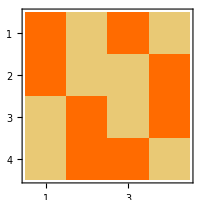

```mathematica
With[{states=VertexList[QuantumCircuitMultiwayGraph[doubleCHSH/*Table["Measure"->i,{i,4}],GraphLayout->"LayeredDigraphEmbedding",EdgeLabels->__tag_:>Framed[tag["Operator"]["CircuitDiagram","WireLabels"->None,"ShowGateLabels"->False,"ShowEmptyWires"->False,FontSize->8,ImageSize->{32,32}],Background->White],PerformanceGoal->"Quality"]][[-16;;,2]]},
MatrixPlot@FullSimplify@Total[Partition[Values@QuantumTensorProduct[#]["Computational"]["Amplitudes"],4]&/@states]
]
```

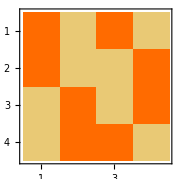

```mathematica
MatrixPlot[Partition[Simplify@Values@(doubleCHSH/*Table["Measure"->i,{i,4}])[]["Amplitudes"],4]]
```

## Playground